# Solovay-Kitaev Algorithm

The Solovay-Kitaev theorem states that an arbitrary single-qubit gate may be constructed approximately to arbitrary accuracy ϵ with a sequence of length n≃Log^α[1/ϵ] of gates from a fixed and finite set. Here, we demonstrate an algorithm that gives a sequence of length  n≃Log^α[1/ϵ] with α≃3.97., assuming a generating set of the Hadamard gate H, octant phase gate T and its inverse T^-1. The Solovay-Kitaev theorem is, of course, far more general, and for algorithms for general cases, see the references at the end of this document.

Solovay | Reprents an elementary generator
TheSolovay | The matrix representation an elementary generator
SolovayChains | Returns the list of all possible sequence of elementary generators
SolovayKitae | Implements the Solovay-Kitaev algorithm

Functions related to the Solovay-Kitaev algorithm.

Load the package.

```mathematica
<<Solovay`
```

## Some Utility Functions

Here are some functions that are used in the algorithm or may be useful to analyse the algorithm.

### BalancedCommutator

```mathematica
?GroupCommutator
```

```mathematica
?BalancedCommutator
```

```mathematica
new=({{0.9689945920647197-0.18643612090113915 ⅈ, 0.15825427836029116+0.035307743526686745 ⅈ}, {-0.15825427836029105+0.035307743526662085 ⅈ, 0.9689945920646759+0.18643612090129802 ⅈ}})
```

{{0.968995-0.186436 ⅈ,0.158254+0.0353077 ⅈ},{-0.158254+0.0353077 ⅈ,0.968995+0.186436 ⅈ}}

```mathematica
MatrixForm/@({uu,vv}=BalancedCommutator[new])
GroupCommutator[uu,vv]-new//Chop//MatrixForm
```

RotationSystem::notuni: Matrix {{0.968995-0.186436 ⅈ,0.158254+0.0353077 ⅈ},{-0.158254+0.0353077 ⅈ,0.968995+0.186436 ⅈ}} is not a unitary matrix; its determinant is 1..

{(0.935676-0.267733 ⅈ | -0.0843935-0.213791 ⅈ
0.0843935-0.213791 ⅈ | 0.935676+0.267733 ⅈ),(0.935676-0.0576092 ⅈ | -0.293097+0.187844 ⅈ
0.293097+0.187844 ⅈ | 0.935676+0.0576092 ⅈ)}

(0 | 0
0 | 0)

```mathematica
MatrixForm/@BalancedCommutator[One[2]]
```

{(1 | 0
0 | 1),(1 | 0
0 | 1)}

```mathematica
Do[
mat=TheEulerRotation@RandomReal[{-1,1}Pi,3];
{V,W}=BalancedCommutator[mat];
gc=Chop@Chop@GroupCommutator[V,W];
Echo[mat-gc//Chop//MatrixForm],
10]
```

(0 | 0
0 | 0)

(0 | 0
0 | 0)

(0 | 0
0 | 0)

«7 more identical outputs»

This is one of the dangerous case.

```mathematica
mat={
{0.6176764285966168+0.19302865391947965 ⅈ,0.6924904732390966+0.31886158877364695 ⅈ},{-0.6924904732390966+0.31886158877364695 ⅈ,0.6176764285966168-0.19302865391947965 ⅈ}
};
mat//MatrixForm
```

(0.617676+0.193029 ⅈ | 0.69249+0.318862 ⅈ
-0.69249+0.318862 ⅈ | 0.617676-0.193029 ⅈ)

```mathematica
{V,W}=BalancedCommutator[mat];
gc=Chop@Chop@GroupCommutator[V,W];
mat-gc//Chop//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
mat=TheRotation[2Pi/3,2];
mat//N//MatrixForm
{V,W}=BalancedCommutator[N@mat];
gc=Chop@Chop@GroupCommutator[V,W];
mat-gc//Chop//MatrixForm
```

(0.5 | -0.866025
0.866025 | 0.5)

(0 | 0
0 | 0)

### Solovay, TheSolovay

```mathematica
?Solovay
```

```mathematica
?TheSolovay
```

```mathematica
ops=Solovay@{-3,3,9,1,2,9,-1}
```

{T^-3,T^3,H,T,T^2,H,T^-1}

```mathematica
MatrixForm/@TheSolovay@ops
```

{(1 | 0
0 | ⅇ^(-(3 ⅈ π)/4)),(1 | 0
0 | ⅇ^((3 ⅈ π)/4)),(1/(√2) | 1/(√2)
1/(√2) | -1/(√2)),(1 | 0
0 | ⅇ^((ⅈ π)/4)),(1 | 0
0 | ⅈ),(1/(√2) | 1/(√2)
1/(√2) | -1/(√2)),(1 | 0
0 | ⅇ^(-(ⅈ π)/4))}

```mathematica
MatrixForm/@TheSolovay@Range[0,7]
```

{(1 | 0
0 | 1),(1 | 0
0 | ⅇ^((ⅈ π)/4)),(1 | 0
0 | ⅈ),(1 | 0
0 | ⅇ^((3 ⅈ π)/4)),(1 | 0
0 | -1),(1 | 0
0 | ⅇ^(-(3 ⅈ π)/4)),(1 | 0
0 | -ⅈ),(1 | 0
0 | ⅇ^(-(ⅈ π)/4))}

```mathematica
MatrixForm@TheSolovay[9]
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

## Exhaustive Search

Before we examine an instance of the Solovay-Kitaev algorithm, here we consider searching the exhaustive list of generator sequences of finite length. It is not so trivial. For example, given a fixed length n, a naive approach is to consider n-tuples of elementary generators H, T, and T^-1, where H and T denotes the Hadamard and octant phase gates, respectively.  It may give, say, sequence {H, H, H} of three Hadamard operators. But it is actually equal to the sequence {H} of single Hadamard operator.

```mathematica
<<Solovay`
```

### Basic Examples

```mathematica
?SolovayChains
```

```mathematica
cc=SolovayChains[4];
Solovay@cc//TableForm
```

T^4 |  |  | 
T^-2 | H | T^-1 | 
T^-2 | H | T^1 | 
T^2 | H | T^-1 | 
T^2 | H | T^1 | 
H | T^-3 |  | 
H | T^3 |  | 
H | T^-1 | H | T^-1
H | T^-1 | H | T^1
H | T^1 | H | T^-1
H | T^1 | H | T^1
T^-3 | H |  | 
T^3 | H |  | 
T^-1 | H | T^-1 | H
T^-1 | H | T^1 | H
T^1 | H | T^-1 | H
T^1 | H | T^1 | H
H | T^-2 | H | 
H | T^2 | H |

```mathematica
chainLength[ch_List]:=Total@Mod[Abs@ch,4,1]
```

```mathematica
chainLength/@cc
```

{4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}

```mathematica
mm=Dot@@@TheSolovay@cc//SimplifyThrough;
```

```mathematica
MatrixForm/@mm
```

{(1 | 0
0 | -1),(1/(√2) | 1/2-ⅈ/2
-ⅈ/(√2) | 1/2+ⅈ/2),(1/(√2) | 1/2+ⅈ/2
-ⅈ/(√2) | -1/2+ⅈ/2),(1/(√2) | 1/2-ⅈ/2
ⅈ/(√2) | -1/2-ⅈ/2),(1/(√2) | 1/2+ⅈ/2
ⅈ/(√2) | 1/2-ⅈ/2),(1/(√2) | -1/2-ⅈ/2
1/(√2) | 1/2+ⅈ/2),(1/(√2) | -1/2+ⅈ/2
1/(√2) | 1/2-ⅈ/2),(1/2 (1-(-1)^(3/4)) | -1/2 ⅈ (-1+(-1)^(1/4))
1/2 (1+(-1)^(3/4)) | -1/2 ⅈ (1+(-1)^(1/4))),(1/2 (1-(-1)^(3/4)) | 1/2 (-1+(-1)^(1/4))
1/2 (1+(-1)^(3/4)) | 1/2 (1+(-1)^(1/4))),(1/2 (1+(-1)^(1/4)) | 1/2 (-1-(-1)^(3/4))
1/2 (1-(-1)^(1/4)) | 1/2 (1-(-1)^(3/4))),(1/2 (1+(-1)^(1/4)) | 1/2 (-ⅈ+(-1)^(1/4))
1/2 (1-(-1)^(1/4)) | 1/2 (ⅈ+(-1)^(1/4))),(1/(√2) | 1/(√2)
-1/2-ⅈ/2 | 1/2+ⅈ/2),(1/(√2) | 1/(√2)
-1/2+ⅈ/2 | 1/2-ⅈ/2),(1/2 (1-(-1)^(3/4)) | 1/2 (1+(-1)^(3/4))
1/2 (ⅈ-(-1)^(3/4)) | 1/2 (-ⅈ-(-1)^(3/4))),(1/2 (1+(-1)^(1/4)) | 1/2 (1-(-1)^(1/4))
1/2 (-1-(-1)^(3/4)) | 1/2 (1-(-1)^(3/4))),(1/2 (1-(-1)^(3/4)) | 1/2 (1+(-1)^(3/4))
1/2 (-1+(-1)^(1/4)) | 1/2 (1+(-1)^(1/4))),(1/2 (1+(-1)^(1/4)) | 1/2 (1-(-1)^(1/4))
1/2 (-ⅈ+(-1)^(1/4)) | 1/2 (ⅈ+(-1)^(1/4))),(1/2-ⅈ/2 | 1/2+ⅈ/2
1/2+ⅈ/2 | 1/2-ⅈ/2),(1/2+ⅈ/2 | 1/2-ⅈ/2
1/2-ⅈ/2 | 1/2+ⅈ/2)}

### Demonstration of the Solovay-Kitaev Theorem

```mathematica
svyDictionary=Solovay`Private`svyDictionary;
```

```mathematica
chainLength[ch_List]:=Total@Mod[Abs@ch,4,1]
```

```mathematica
mat=TheRotation[Pi/4,1];
mat//MatrixForm
```

(Cos[π/8] | -ⅈ Sin[π/8]
-ⅈ Sin[π/8] | Cos[π/8])

```mathematica
EchoTiming[cc=svyDictionary[18];]
Length[cc]
```

1.63525

21572

```mathematica
EchoTiming[ee=Sort@Map[Norm[#-mat]&,Values@cc];]
ListLogLogPlot[ee,PlotRange->All,Joined->True]
```

0.22826

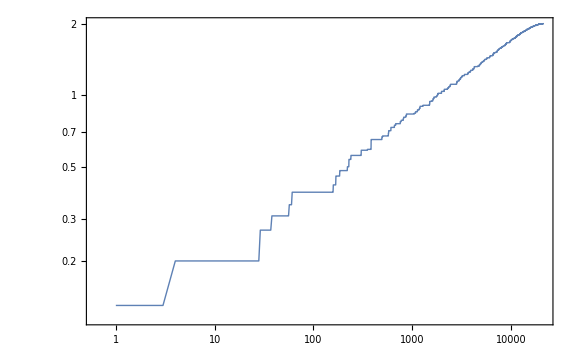

```mathematica
ee[[;;10]]
```

{0.130161,0.130161,0.130161,0.200389,0.200389,0.200389,0.200389,0.200389,0.200389,0.200389}

```mathematica
min=MinimalBy[cc,Norm[#-mat]&];
KeyGroupBy[min,chainLength]
```

<|18→<|{-2,9,1,9,-1,9,-1,9,1,9,-1,9,1,9,1,9,1}→{{0.875-0.0517767 ⅈ,-0.0517767-0.478553 ⅈ},{0.0517767-0.478553 ⅈ,0.875+0.0517767 ⅈ}}|>|>

```mathematica
data={
{-Log@0.200389,12},
{-Log@0.130161,18},
{-Log@0.0229649,22},
{-Log@0.0229649,24}
}
```

{{1.60749,12},{2.03898,18},{3.77379,22},{3.77379,24}}

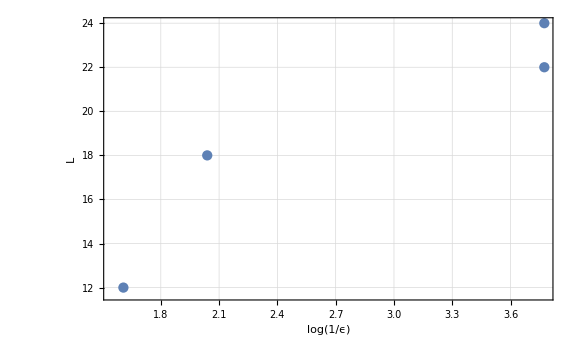

```mathematica
ListPlot[data,FrameLabel->{Log[1/ϵ],"L"}]
```

## Solovay-Kitaev Algorithm

Here, an implementation of the Solovay-Kitaev algorithm is demonstrated.

```mathematica
<<Solovay`
```

### Function SolovayKitaev

```mathematica
?SolovayKitaev
```

```mathematica
in=TheRotation[Pi/4,2];
in//MatrixForm
```

(Cos[π/8] | -Sin[π/8]
Sin[π/8] | Cos[π/8])

```mathematica
SolovayKitaev[in,0]
```

1.61565

{{9,-1,9,1,9,1,9,-1,9,1,9,-1,9,-1,9,1},{{0.875+0.0517767 ⅈ,-0.478553-0.0517767 ⅈ},{0.478553-0.0517767 ⅈ,0.875-0.0517767 ⅈ}}}

```mathematica
EchoTiming[{chain,out}=SolovayKitaev[in,3];]
```

1.5469

```mathematica
tmp=Dot@@N[TheSolovay@chain];
tmp//MatrixForm
```

(0.923907-0.000898188 ⅈ | -0.382615+0.000219076 ⅈ
0.382615+0.000219076 ⅈ | 0.923907+0.000898188 ⅈ)

```mathematica
tmp-out//Chop//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
Norm[in-out]
```

0.000927475

### Demonstrations

```mathematica
in=TheRotation[Pi/4,2];
in//MatrixForm
```

(Cos[π/8] | -Sin[π/8]
Sin[π/8] | Cos[π/8])

```mathematica
EchoTiming[{chain,out}=SolovayKitaev[in,2];]
```

1.6293

2.2784

```mathematica
in-out//Norm
```

0.0172581

```mathematica
Length[chain]
```

410

```mathematica
Solovay@chain
```

{H,T,H,T^-1,H,T^-1,H,T,H,T,H,T,H,T^-1,H,T^-1,T^2,H,T^-1,H,T,H,T,H,T^-1,H,T^-1,H,T^-1,H,T,H,T^-1,T,H,T,H,T^-1,H,T^-1,H,T^-1,H,T,H,T,H,T^-1,H,T,H,T^-1,H,T,H,T,H,T,H,T^-1,H,T^-1,H,T,H,T^-2,T,H,T,H,T^-1,H,T^-1,H,T,H,T^-1,H,T^-1,H,T,H,H,T,H,T^-1,H,T,H,T,H,T^-1,H,T^-1,H,T^-1,H,T,T^-2,H,T^-1,H,T,H,T^-1,H,T^-1,H,T,H,T,H,T,H,T,T^-1,H,T,H,T,H,T,H,T^-1,H,T^-1,H,T,H,T^-1,H,T^-1,H,T^-1,H,T^-1,H,T^-1,H,T,H,T,H,T^-1,H,T,H,T^2,H,T,H,T^-1,H,T^-1,H,T^-1,H,T,H,T,H,T^-1,H,T,H,T^-1,H,T,H,T,H,T^-1,H,T,H,T,H,T^-1,H,T^-1,T^2,H,T^-1,H,T,H,T,H,T^-1,H,T^-1,H,T^-1,H,T,H,T^-1,H,T,H,T^-1,H,T^-1,H,T,H,T,H,T,H,T^-1,H,T^-1,T,H,T^-1,H,T,H,T,H,T,H,T^-1,H,T^-1,H,T,H,T^-2,T,H,T,H,T^-1,H,T^-1,H,T^-1,H,T,H,T,H,T^-1,H,T^-1,H,T,H,T^-1,H,T^-1,H,T,H,T,H,T,H,T^-1,H,T^-2,H,T^-1,H,T,H,T^-1,H,T^-1,H,T,H,T,H,T,H,T,H,T,H,T^-1,H,T,H,T,H,T^-1,H,T^-1,H,T^-1,H,T,T^-1,H,T^-1,H,T^-1,H,T^-1,H,T,H,T,H,T^-1,H,T,H,T^2,T^-1,H,T,H,T,H,T,H,T^-1,H,T^-1,H,T,H,T^-1,H,T^-2,H,T^-1,H,T,H,T^-1,H,T^-1,H,T,H,T,H,T,H,T,H,T,H,T^-1,H,T^-1,H,T^-1,H,T,H,T,H,T^-1,H,T,T^-1,H,T^-1,H,T^-1,H,T^-1,H,T,H,T,H,T^-1,H,T,H,T^2,T^-1,H,T,H,T^-1,H,T^-1,H,T,H,T,H,T,H,T^-1,H,H,T^-1,H,T,H,T,H,T^-1,H,T,H,T^-1,H,T^-1,H,T}

```mathematica
EchoTiming[{chain,out}=SolovayKitaev[in,4];]
```

RotationSystem::notuni: Matrix {{1.+0.000913655 ⅈ,-0.0000739851+0.000141322 ⅈ},{0.0000739851+0.000141322 ⅈ,1.-0.000913655 ⅈ}} is not a unitary matrix; its determinant is 1..

4.33545

```mathematica
Norm[in-out]
```

0.0000813475

Related Guides

Quantum Computation and Information

Related Tech Notes

A Quantum Playbook

Quantum Computation and Information: Overview

Related Links

A. W. Harrow, Be. Recht, and I. L. Chuang, Journal of Mathematical Physics 43, 4445 (2002), “Effective discrete approximations of quantum gates”.

C. Dawson and M. Nielsen, Quantum Information and Computation 6, 81 (2006), “The Solovay-Kitaev algorithm”.

M. Nielsen and I. L. Chuang (2022), Quantum Computation and Quantum Information (Cambridge University Press, 2011), Appendix 3.

## Metadata

### Categorization

Tech Note

QuantumPlaybook

QuantumPlaybook`

QuantumPlaybook/tutorial/SolovayKitaevAlgorithm

### Keywords

Solovay-Kitaev theorem

Solovay-Kitaev algorithm